```mathematica
e=0.0933941
c=(2.2792×10^{16}×π×2.269)/(59.4× 10^6)
d=(249.23×10^6(1-0.0933941))/0.0933941
```

0.0933941

{2.73515×10^9}

2.41935×10^9

```mathematica
print[d]
```

print[2.41935×10^9]

```mathematica
s=NDSolve[{((e×d)^2× θ'[t])/(2(1+e×Cos[θ[t]])^2)==2.735182249420772*^9,θ[0]==0},θ,{t,0,5.94*10^7}]
```

{{θ→InterpolatingFunction[…]}}

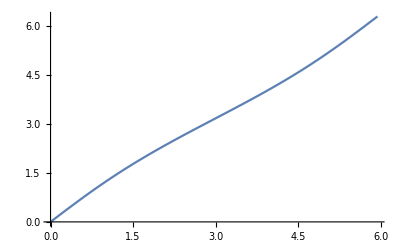

```mathematica
Plot[Evaluate[θ[t]/.s],{t,0,5.94×10^7},PlotRange->All]
```

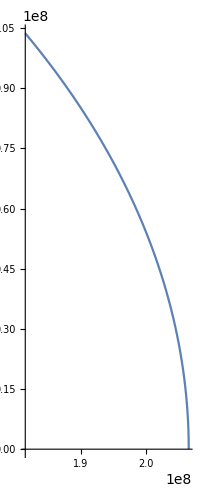

```mathematica
curv=ParametricPlot[Evaluate[CoordinateTransform["Polar"->"Cartesian",{(e×d)/(1+e×Cos[θ[t]]),θ[t]}]/.s],{t,0,5.94×10^6}]
```

```mathematica
u[t_]:=First[Evaluate[First[CoordinateTransform["Polar"->"Cartesian",{(e×d)/(1+e×Cos[θ[t]]),θ[t]}]]/.s]]
v[t_]:=First[Evaluate[Last[CoordinateTransform["Polar"->"Cartesian",{(e×d)/(1+e×Cos[θ[t]]),θ[t]}]]/.s]]
```

```mathematica
First[Evaluate[First[CoordinateTransform["Polar"->"Cartesian",{(e×d)/(1+e×Cos[θ[t]]),θ[t]}]]/.s]]
```

(3.42519×10^7 Cos[InterpolatingFunction[…][t]])/(1+0.0933941 Cos[InterpolatingFunction[…][t]])

```mathematica
Animate[Show[curv,Graphics[{PointSize[Large],Red,Point[{u[T],v[T]}]}]],{T,0,5.94×10^6}]
```